```mathematica
Module[{Psat1,Psat2,γ1,γ2,Px,Py,A12,A21},

Psat1[T_]:=10^(4.-1150.53/(T+224.2));
Psat2[T_]:=10^(4.05-1355/(T+209.4));

(*Px[T_,x_]:=x*Psat1[T]+(1-x)*Psat2[T];
Py[T_,x_]:=(x/Psat1[T]+(1-x)/Psat2[T])^-1;*)
A12=0;
A21=0.8;

γ1[x_]:=Exp[(1-x)^2*(A12+2*(A21-A12)*x)];
γ2[x_]:=Exp[x^2*(A21+2*(A12-A21)*(1-x))];

Px[T_,x_]:=γ1[x]*x*Psat1[T]+γ2[x]*(1-x)*Psat2[T];
Py[T_,x_]:=(x/(γ1[x]*Psat1[T])+(1-x)/(γ2[x]*Psat2[T]))^-1;

(*Show[
Table[Plot[{Px[temp,x],Py[temp,x]},{x,0,1},PlotStyle->{{Thick,Opacity[temp/90-0.5],Blue},{Thick,Opacity[temp/90-0.5],Purple}}],{temp,90,110,5}],
PlotRange->All,
Frame->True,
FrameLabel->{Style["component 1 mole fraction",17],Style["pressure (bar)",17]},
LabelStyle->{Black,13},
ImageSize->450]*)
Plot3D[{Px[T,x],Py[T,x]},{x,0,1},{T,90,100},ImageSize->500]
]
```

-Graphics3D-

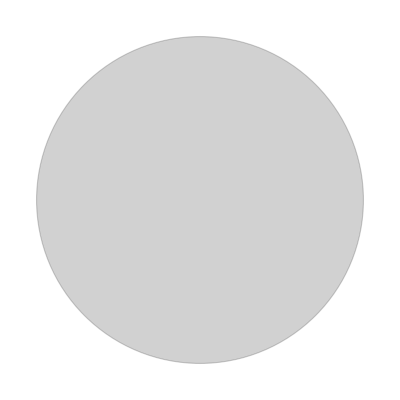
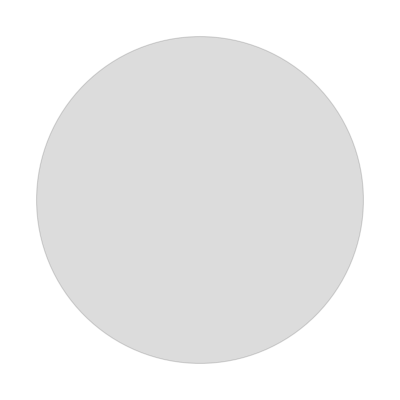
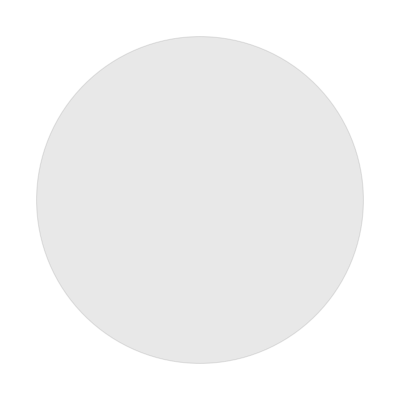
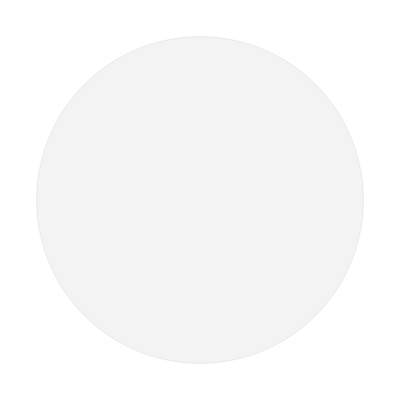
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[{EdgeForm[Thick],Opacity[1-i/110],Disk[]}],{i,90,110,5}]
```

```mathematica
N@90/110
```

0.818182

```mathematica
(*,
Row[{Style["ideal",14],Spacer[10],Control[{{A12,0,Row[{"(",Subscript[Style["A",Italic],"12"],")"}]},0,2,0.1,Appearance->"Labeled"}],Style["non-ideal",14]}],
Row[{Style["ideal",14],Spacer[10],Control[{{A21,0,Row[{"(",Subscript[Style["A",Italic],"21"],")"}]},0,2,0.1,Appearance->"Labeled"}],Style["non-ideal",14]}]*)
```

```mathematica
(*γ1[x_]:=Exp[(1-x)^2*(A12+2*(A21-A12)*x)];
γ2[x_]:=Exp[x^2*(A21+2*(A12-A21)*(1-x))];

Px[x_]:=γ1[x]*x*Psat1+γ2[x]*(1-x)*Psat2;
Py[x_]:=(x/(γ1[x]*Psat1)+(1-x)/(γ2[x]*Psat2))^-1;*)
```